Problem III : already producing with cannibalization effect η

## Benchmark Model

```mathematica
Simplify@Solve[x==d1(-(1-α k0)k0/r+(2η k0 k)x/(r-μ))/(2η k0 k/(r-μ)),x]
```

{{x→-(d1 (-1+k0 α) (r-μ))/(2 (-1+d1) k r η)}}

onde pi0 =(1-  α k0)k0

```mathematica
Simplify@(-(1-α k0)k0/r+2η k0 k/(r-μ)(-(d1 (-1+k0 α) (r-μ))/(2 (-1+d1) k r η)))
```

-(k0 (-1+k0 α))/((-1+d1) r)

### Problema τ2

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; (*check!*)
aB2[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:= ((k0 (1-k0 α))/((-1+d1[μ,σ,r])  r))xx^(-d1[μ,σ,r]);
g2[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=((θ- α k) k -2η k0 k)xx /(r-μ); (*check!*)
hB2[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=(θ- α k) k/(r-μ)xx- (1-  α k0)k0/r; (*check!*)
xxB2[r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=(d1[μ,σ,r] (1-k0 α) (r-μ))/(2 (-1+d1[μ,σ,r] ) k r η);

(*F[y_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=hB[y,r,μ,σ,θ,k0,α,δ,k]-(aB[y,r,μ,σ,θ,k0,α,δ,k,η]* y^d1[μ,σ,r]+g[y ,r,μ,σ,θ,k0,α,δ,k,η]);*)
```

```mathematica
Simplify@aB[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1
```

(2^dd1 k k0 η ((dd1 (1-k0 α) (r-μ))/((-1+dd1) k r η))^(1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2))/(dd1 (r-μ))

```mathematica
Manipulate[Show[Plot[{
(*hB2[ xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,r,μ,σ,θ,k0,α,δ,k]-(aB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])+g2[x ,r,μ,σ,θ,k0,α,δ,k,η]),*)
(aB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])+g2[x ,r,μ,σ,θ,k0,α,δ,k,η]),
hB2[x,r,μ,σ,θ,k0,α,δ,k]
 } 
,{x,0.01,100},AxesLabel->{"x","HJB"},AxesOrigin->{0,0},PlotLegends->"Placeholder"],
Epilog->{Black, PointSize[0.02],
(*Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,F[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]
}],*)
Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]
}]
}],
{r,0.001,1},{μ,-r,r},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

### Problema τ1

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; (*check!*)
aB1[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:= aB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]+((θ- α k) k -2η k0 k)xx ^(1-d1[μ,σ,r])/(r-μ)-δ k xx^(-d1[μ,σ,r]);
(* g2[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=((θ- α k) k -2η k0 k)xx /(r-μ); *)
hB1[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=aB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]xx^(d1[μ,σ,r])+((θ- α k) k -2η k0 k)xx /(r-μ)-δ k ;
xxB1[r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])(δ k(r-μ))/((θ- α k) k -2η k0 k);

F[y_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=hB1[y,r,μ,σ,θ,k0,α,δ,k,η]-(aB1[y,r,μ,σ,θ,k0,α,δ,k,η]* y^d1[μ,σ,r]);
```

```mathematica
Simplify@aB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1 //.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->1-dd1
```

(2^dd1 k k0 η ((dd1 (1-k0 α) (r-μ))/((-1+dd1) k r η))^(1-dd1))/(dd1 (r-μ))

```mathematica
Simplify@aB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1 //.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->1-dd1
```

(2^dd1 k k0 η ((dd1 (1-k0 α) (r-μ))/((-1+dd1) k r η))^(1-dd1))/(dd1 (r-μ))+(k (-k α-2 k0 η+θ) ((dd1 δ (r-μ))/((-1+dd1) (-k α-2 k0 η+θ)))^(1-dd1))/(r-μ)-k δ ((dd1 δ (r-μ))/((-1+dd1) (-k α-2 k0 η+θ)))^-dd1

```mathematica
Manipulate[Show[Plot[{
(*hB2[ xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,r,μ,σ,θ,k0,α,δ,k]-(aB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])+g2[x ,r,μ,σ,θ,k0,α,δ,k,η]),*)
(aB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])),
hB1[x,r,μ,σ,θ,k0,α,δ,k,η],
hB2[x,r,μ,σ,θ,k0,α,δ,k]-δ k 
 } 
,{x,0.01,10},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->"Placeholder"],
Graphics[{PointSize[0.02],Cyan,Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.02],Blue,Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
],
(*Epilog->{Cyan, PointSize[0.02],
Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k
}]
}],*)
{r,0.001,1},{μ,-r,r},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

```mathematica
σ=0.005;
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
k0=90;
η=α/2;
```

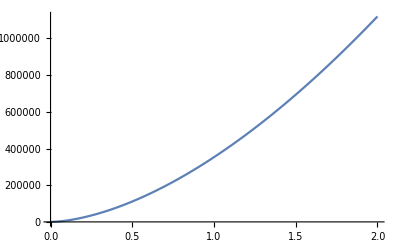

```mathematica
Plot[aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r], {x,0,2}]
```

```mathematica
aB[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:= (δ  k + (1-  α k0)k0/r  )xx^(-d1[μ,σ,r])/(d1[μ,σ,r]-1);
hB[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=(θ- α k) k/(r-μ)xx-( δ  k + (1-  α k0)k0/r  );
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2];
xxB[r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])( δ  k + (1-  α k0)k0/r  )/(θ- α k) (r-μ)/k;
```

```mathematica
Manipulate[Show[Plot[{
(*hB2[ xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,r,μ,σ,θ,k0,α,δ,k]-(aB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])+g2[x ,r,μ,σ,θ,k0,α,δ,k,η]),*)
(aB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])),
aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r],
hB1[x,r,μ,σ,θ,k0,α,δ,k,η],
hB2[x,r,μ,σ,θ,k0,α,δ,k]-δ k,
F[x,r,μ,σ,θ,k0,α,δ,k,η] 
(*hB[x,r,μ,σ,θ,k0,α,δ,k]*)
 } 
,{x,0.01,10},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->"Placeholder", PlotStyle->{Lighter[Blue,0.4],Blue, Darker[Cyan],Cyan,{Dashing[0.01],Red}}],
Graphics[{PointSize[0.02],Lighter[Magenta],Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.02],Darker[Magenta],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}],
Graphics[{PointSize[0.02],Black,Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB2[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
],
(*Epilog->{Cyan, PointSize[0.02],
Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k
}]
}],*)
{r,0.001,1},{μ,-r,r},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

```mathematica
F[x_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:= Which[
η<(1-α k0)(θ-α k)/(2(δ k r+(1-α k0)k0)),
Which[
x<xxB1[r,μ,σ,θ,k0,α,δ,k,η](*&&η<(1-α k0)(θ-α k)/(2(δ k r+(1-α k0)k0))*),
aB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r]),
x>=xxB1[r,μ,σ,θ,k0,α,δ,k,η]&& x<xxB2[r,μ,σ,θ,k0,α,δ,k,η](*&&η<(1-α k0)(θ-α k)/(2(δ k r+(1-α k0)k0))*),
hB1[x,r,μ,σ,θ,k0,α,δ,k,η],
x>=xxB2[r,μ,σ,θ,k0,α,δ,k,η],
hB2[x,r,μ,σ,θ,k0,α,δ,k]-δ k],
η>=(1-α k0)(θ-α k)/(2(δ k r+(1-α k0)k0)),
Which[
x<xxB[r,μ,σ,θ,k0,α,δ,k] ,
aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r],
x>=xxB[r,μ,σ,θ,k0,α,δ,k] ,
hB2[x,r,μ,σ,θ,k0,α,δ,k]-δ k]
]
```

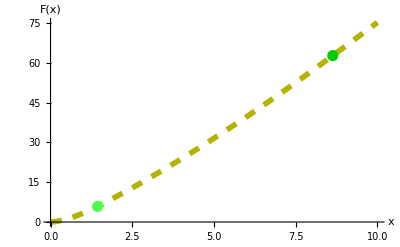

```mathematica
Module[{r=0.85,μ=0.45, k0=51.5, δ=0.95, k=2.5,θ=1.5, σ=0.6, α=0.015,η=0.007},
Show[Plot[F[x,r,μ,σ,θ,k0,α,δ,k,η],{x,0.01,10},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->"Placeholder", PlotStyle->{{Dashing[0.02],Thickness[0.01],Darker[Yellow,.3]}}],
Graphics[{PointSize[0.02],Lighter[Green,0.3],Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.02],Darker[Green,0.2],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
(*Graphics[{PointSize[0.02],Black,Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB2[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]*)
]]
```

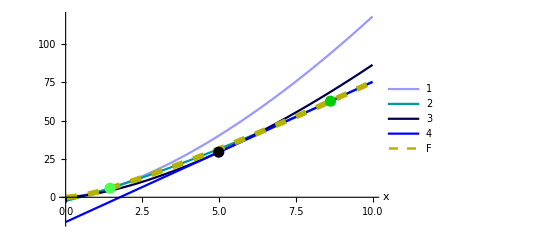

```mathematica
Module[{r=0.85,μ=0.45, k0=51.5, δ=0.95, k=2.5,θ=1.5, σ=0.6, α=0.015,η=0.007},
Show[Plot[{
(aB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])),
hB1[x,r,μ,σ,θ,k0,α,δ,k,η],
aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r],
hB2[x,r,μ,σ,θ,k0,α,δ,k]-δ k,
F[x,r,μ,σ,θ,k0,α,δ,k,η] 
 } 
,{x,0.01,10},AxesLabel->{"x"," "},AxesOrigin->{0,0}, PlotStyle->{Lighter[Blue,0.6],Darker[Cyan,0.4],Darker[Blue,0.7],Blue,{Dashing[0.02],Thickness[0.01],Darker[Yellow,.3]}},
PlotLegends->Placed[
(* {"a_(1, A)x_(1, A)","a_(1, R)x_(1, R)","a_2x_2","h","F"} *)
{"1","2","3","4","F"}, {Left ,Top}]
],
Graphics[{PointSize[0.02],Lighter[Green,0.3],Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.02],Darker[Green,0.2],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}],
Graphics[{PointSize[0.02],Black,Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB2[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
]]
```

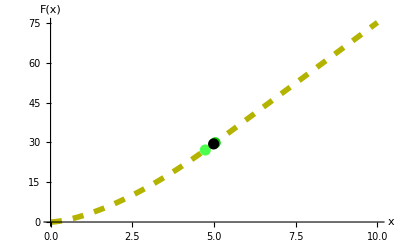

```mathematica
Module[{r=0.85,μ=0.45, k0=51.5, δ=0.95, k=2.5,θ=1.5, σ=0.6, α=0.015,η=0.012},
Show[Plot[F[x,r,μ,σ,θ,k0,α,δ,k,η],{x,0.01,10},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->"Placeholder", PlotStyle->{{Dashing[0.02],Thickness[0.01],Darker[Yellow,.3]}}],
Graphics[{PointSize[0.02],Lighter[Green,0.3],Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.02],Darker[Green,0.2],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}],
Graphics[{PointSize[0.02],Black,Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB2[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
]]
```

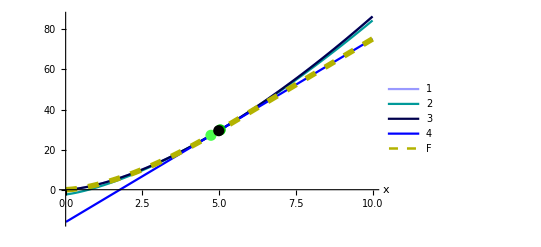

```mathematica
Module[{r=0.85,μ=0.45, k0=51.5, δ=0.95, k=2.5,θ=1.5, σ=0.6, α=0.015,η=0.012},
Show[
Plot[{
(aB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])),
hB1[x,r,μ,σ,θ,k0,α,δ,k,η],
aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r],
hB2[x,r,μ,σ,θ,k0,α,δ,k]-δ k,
F[x,r,μ,σ,θ,k0,α,δ,k,η] 
 } 
,{x,0.01,10},AxesLabel->{"x"," "},AxesOrigin->{0,0}, PlotStyle->{Lighter[Blue,0.6],Darker[Cyan,0.4],Darker[Blue,0.7],Blue,{Dashing[0.02],Thickness[0.01],Darker[Yellow,.3]}},
PlotLegends->Placed[
(* {"a_(1, A)x_(1, A)","a_(1, R)x_(1, R)","a_2x_2","h","F"} *)
{"1","2","3","4","F"}, {Left ,Top}]
],
Graphics[{PointSize[0.02],Lighter[Green,0.3],Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.02],Darker[Green,0.2],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}],
Graphics[{PointSize[0.02],Black,Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB2[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
]]
```

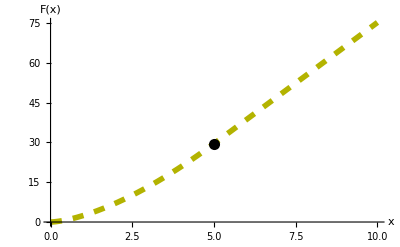

```mathematica
Module[{r=0.85,μ=0.45, k0=51.5, δ=0.95, k=2.5,θ=1.5, σ=0.6, α=0.015,η=0.013},
Show[Plot[F[x,r,μ,σ,θ,k0,α,δ,k,η],{x,0.01,10},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->"Placeholder", PlotStyle->{{Dashing[0.02],Thickness[0.01],Darker[Yellow,.3]}}],
(*Graphics[{PointSize[0.02],Lighter[Green,0.5],Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.02],Darker[Green,0],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}],*)
Graphics[{PointSize[0.02],Black,Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB2[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
]]
```

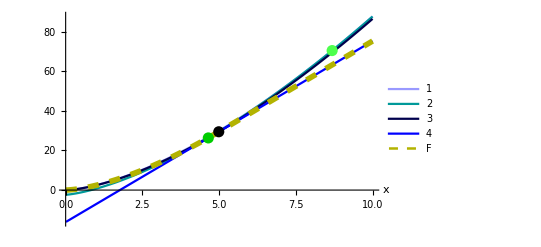

```mathematica
Module[{r=0.85,μ=0.45, k0=51.5, δ=0.95, k=2.5,θ=1.5, σ=0.6, α=0.015,η=0.013},
Show[Plot[{
(aB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])),
hB1[x,r,μ,σ,θ,k0,α,δ,k,η],
aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r],
hB2[x,r,μ,σ,θ,k0,α,δ,k]-δ k,
F[x,r,μ,σ,θ,k0,α,δ,k,η] 
 } 
,{x,0.01,10},AxesLabel->{"x"," "},AxesOrigin->{0,0}, PlotStyle->{Lighter[Blue,0.6],Darker[Cyan,0.4],Darker[Blue,0.7],Blue,{Dashing[0.02],Thickness[0.01],Darker[Yellow,.3]}},
PlotLegends->Placed[
(* {"a_(1, A)x_(1, A)","a_(1, R)x_(1, R)","a_2x_2","h","F"} *)
{"1","2","3","4","F"}, {Left ,Top}]
],
Graphics[{PointSize[0.02],Lighter[Green,0.3],Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.02],Darker[Green,0.2],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}],
Graphics[{PointSize[0.02],Black,Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB2[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
]]
```

```mathematica
Module[{r=0.85,μ=0.45, k0=51.5, δ=0.95, k=2.5,θ=1.5, σ=0.6, α=0.015,η=0.013},(1-α k0)(θ-α k)/(2(δ k r+(1-α k0)k0))]
```

0.0121121

```mathematica
SetDirectory[NotebookDirectory[]];
f=Table[
Module[{r=0.85,μ=0.45, k0=51.5, δ=0.95, k=2.5,θ=1.5, σ=0.6, α=0.015},
Show[Plot[{
(aB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]*x^(d1[μ,σ,r])),
hB1[x,r,μ,σ,θ,k0,α,δ,k,η],
aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r],
hB2[x,r,μ,σ,θ,k0,α,δ,k]-δ k,
F[x,r,μ,σ,θ,k0,α,δ,k,η] 
 } 
,{x,0.01,10},AxesLabel->{"x"," "},AxesOrigin->{0,0}, PlotStyle->{Lighter[Blue,0.6],Darker[Cyan,0.4],Darker[Blue,0.7],Blue,{Dashing[0.02],Thickness[0.01],Darker[Yellow,.3]}},
PlotLegends->Placed[
(* {"a_(1, A)x_(1, A)","a_(1, R)x_(1, R)","a_2x_2","h","F"} *)
{"1","2","3","4","F"}, {Left ,Top}]
],
Graphics[{PointSize[0.03],Lighter[Green,0.3],Point[{xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,hB1[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k,η]}]}],
Graphics[{PointSize[0.03],Lighter[Brown,0.1],Point[{xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,hB2[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r,μ,σ,θ,k0,α,δ,k]-δ k}]}],
Graphics[{PointSize[0.02],Black,Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB2[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-δ k}]}]
]],
{η,0.007,0.014,0.001}];
```

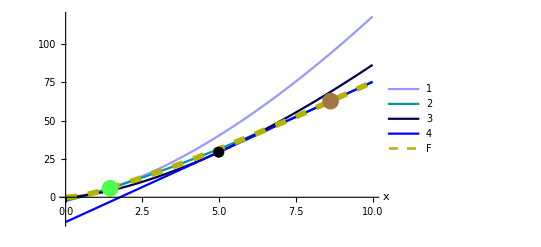
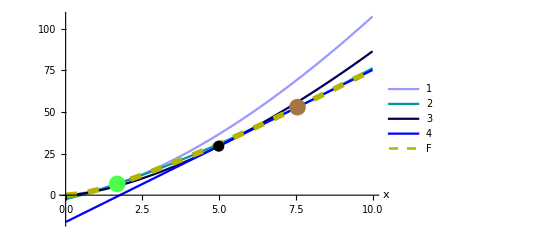
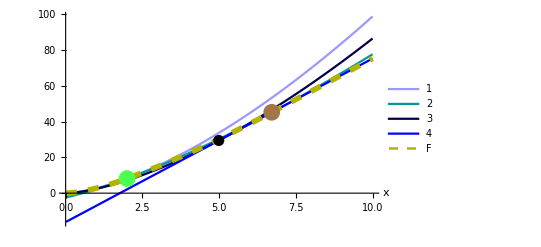
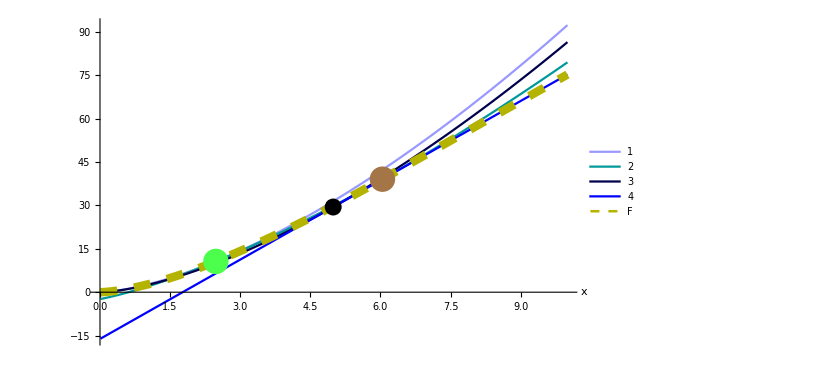
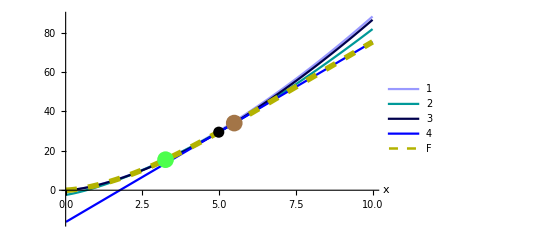
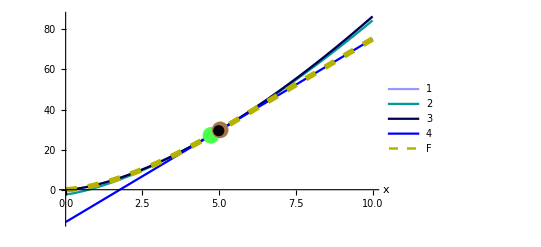
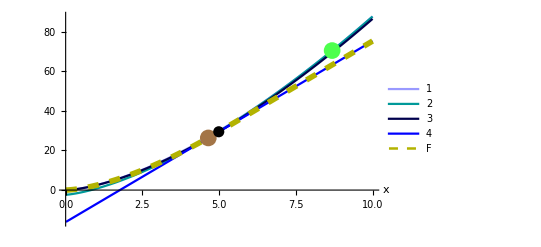
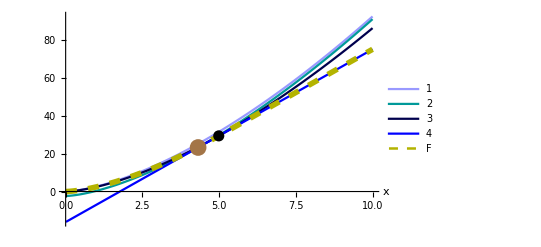

```mathematica
f
```

```mathematica
Export["f.png",f,"VideoFrames"];
```

## Comparative Statics x^*_2

```mathematica
xxB2[r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=(d1[μ,σ,r] (1-k0 α) (r-μ))/(2 (-1+d1[μ,σ,r] ) k r η);
```

```mathematica
D[1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2,r]
```

1/(√((1/2-μ/σ^2)^2+(2 r)/σ^2) σ^2)

```mathematica
Simplify@D[((-1+k0 α) (2 r^2-2 r μ-(-1+dd1) dd1 μ √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2))/(2 (-1+dd1)^2 k r^2 η √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2),dd1]
```

((-1+k0 α) (-4 r^2+4 r μ+(-1+dd1) μ √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2))/(2 (-1+dd1)^3 k r^2 η √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)

```mathematica
σ=0.05;
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
k0=90;
η=0.007;
```

#### - r

```mathematica
Simplify[D[xxB2[r,μ,σ,θ,k0,α,δ,k,η],r]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

((-1+k0 α) (2 r^2-2 r μ-(-1+dd1) dd1 μ √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2))/(2 (-1+dd1)^2 k r^2 η √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)

```mathematica
Manipulate[Show[Plot[xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,
{r,0.01,10},AxesLabel->{"r","x*"},AxesOrigin->{0,0},PlotLegends->"Placeholder"]],
{r,0.001,1},{μ,-r,r},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

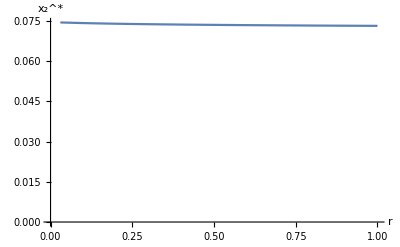

```mathematica
Show[Plot[{xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{r,μ,1},PlotLegends->"Placeholder",AxesOrigin->{0,0}],AxesLabel->{"r","x_2^*"}]
```

#### - μ

```mathematica
Simplify[D[xxB2[r,μ,σ,θ,k0,α,δ,k,η],μ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

((-1+k0 α) (-2 μ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2+(-1+dd1) dd1 √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^4+r (2 μ-(1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)))/(2 (-1+dd1)^2 k r η √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^4)

```mathematica
Manipulate[Show[Plot[{xxB2[r,μ,σ,θ,k0,α,δ,k,η],(r-μ)(2μ-(1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) )σ^2)+(-1+d1[μ,σ,r])d1[μ,σ,r] √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^4},{μ,-r,r},AxesLabel->{"μ","x*"},AxesOrigin->{0,0},PlotLegends->"Placeholder"]],
{r,0.001,1},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

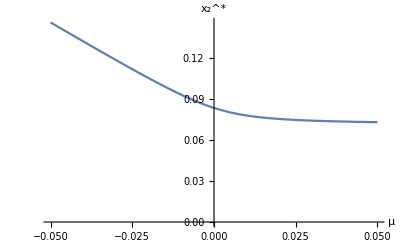

```mathematica
Show[Plot[{xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{μ,-r,r},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"μ","x_2^*"}](*,
Graphics[{PointSize[0.02],Black,Point[{σ^2/2 ,xxB2[r,σ^2/2, σ,θ,k0,α,δ,k,η]}]}]*)
]
```

#### - σ

```mathematica
Simplify[D[xxB2[r,μ,σ,θ,k0,α,δ,k,η],σ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

-((-1+k0 α) (-r+μ) (-2 μ^2-2 r σ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))/((-1+dd1)^2 k r η √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^5)

```mathematica
Manipulate[Show[Plot[xxB2[r,μ,σ,θ,k0,α,δ,k,η] ,{σ,0.001,1},AxesLabel->{"σ","x*"},AxesOrigin->{0,0},PlotLegends->"Placeholder"]],
{r,0.001,1},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{μ,-r,r},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

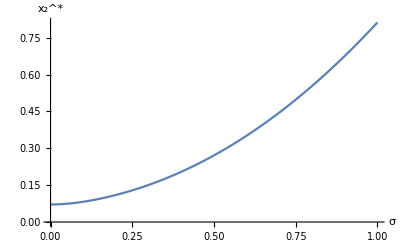

```mathematica
Show[Plot[{xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{σ,0,1},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"σ","x_2^*"}]
]
```

#### - α

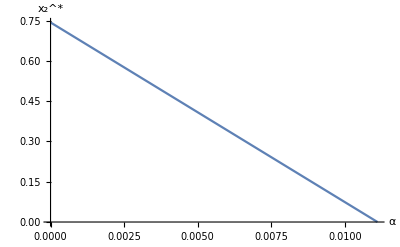

```mathematica
Show[Plot[{xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{α,0,Min[{θ/k,1/k0}]},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"α","x_2^*"}]
]
```

#### - η

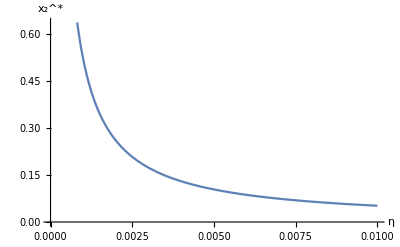

```mathematica
Show[Plot[{xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{η,0,α},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"η","x_2^*"}]
]
```

#### - K0

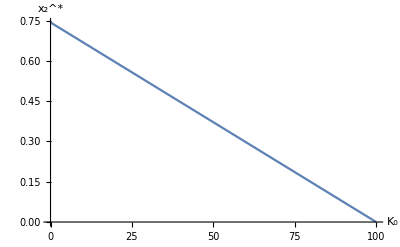

```mathematica
Show[Plot[{xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{k0,0,1/α},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"K_0","x_2^*"}]
]
```

#### - K

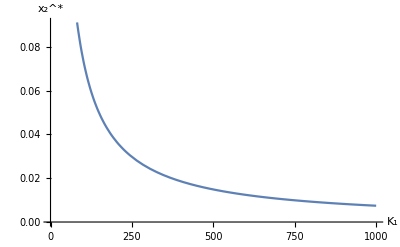

```mathematica
Show[Plot[{xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{k,0,θ/α},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"K_1","x_2^*"}]
]
```

## Comparative Statics

```mathematica
xxB1[r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])(δ k(r-μ))/((θ- α k) k -2η k0 k);
```

#### - r

```mathematica
Simplify[D[xxB1[r,μ,σ,θ,k0,α,δ,k,η],r]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(δ (2 r-2 μ-(-1+dd1) dd1 √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2))/((-1+dd1)^2 (k α+2 k0 η-θ) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)

```mathematica
Manipulate[Show[Plot[xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,
{r,0.01,10},AxesLabel->{"r","x*"},AxesOrigin->{0,0},PlotLegends->"Placeholder"]],
{r,0.001,1},{μ,-r,r},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

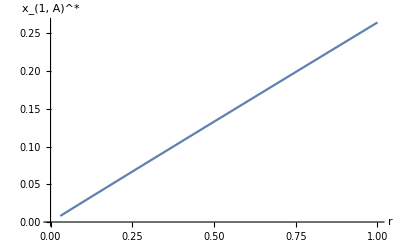

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{r,μ,1},PlotLegends->"Placeholder",AxesOrigin->{0,0}],AxesLabel->{"r","x_(1, A)^*"}]
```

#### - μ

```mathematica
Simplify[D[xxB1[r,μ,σ,θ,k0,α,δ,k,η],μ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(δ (-2 μ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2+(-1+dd1) dd1 √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^4+r (2 μ-(1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)))/((-1+dd1)^2 (k α+2 k0 η-θ) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^4)

```mathematica
Manipulate[Show[Plot[xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,{μ,-r,r},AxesLabel->{"μ","x*"},AxesOrigin->{0,0},PlotLegends->"Placeholder"]],
{r,0.001,1},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

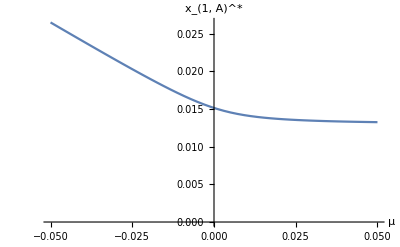

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{μ,-r,r},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"μ","x_(1, A)^*"}]]
```

#### - σ

```mathematica
Simplify[D[xxB1[r,μ,σ,θ,k0,α,δ,k,η],σ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

-(2 δ (-r+μ) (-2 μ^2-2 r σ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))/((-1+dd1)^2 (k α+2 k0 η-θ) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^5)

```mathematica
Manipulate[Show[Plot[xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,{σ,0.001,1},AxesLabel->{"σ","x*"},AxesOrigin->{0,0},PlotLegends->"Placeholder"]],
{r,0.001,1},{k0,0.001,100},{δ,0.001,1},{k,1,10},{θ,1,10},{μ,-r,r},{α,0.001,Min[1/k0,θ/k]},{η,0.001,α-0.001}]
```

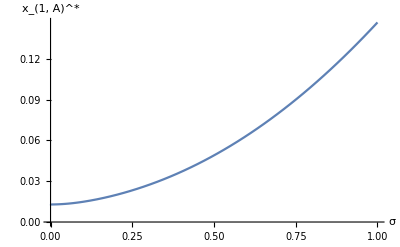

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{σ,0,1},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"σ","x_(1, A)^*"}]]
```

#### - K0

```mathematica
Simplify[D[xxB1[r,μ,σ,θ,k0,α,δ,k,η],k0]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(2 dd1 δ η (r-μ))/((-1+dd1) (k α+2 k0 η-θ)^2)

```mathematica
Manipulate[Show[Plot[xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,{k0,0.001,1/α},AxesLabel->{"k0","x*"},AxesOrigin->{0,0},PlotLegends->"Placeholder"]],
{r,0.001,1},{σ,0.001,1},{δ,0.001,1},{k,1,10},{θ,1,10},{μ,-r,r},{α,0.001,θ/k},{η,0.001,α-0.001}]
```

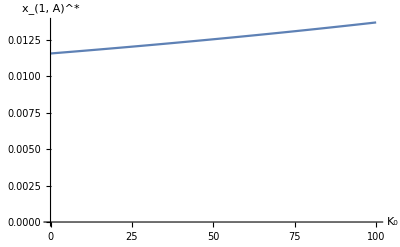

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{k0,0,1/α},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"K_0","x_(1, A)^*"}]
]
```

#### - K

```mathematica
Simplify[D[xxB1[r,μ,σ,θ,k0,α,δ,k,η],k]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(dd1 α δ (r-μ))/((-1+dd1) (k α+2 k0 η-θ)^2)

```mathematica
Manipulate[Show[Plot[xxB1[r,μ,σ,θ,k0,α,δ,k,η] ,{k,0.001,θ/α},AxesLabel->{"k1","x*"},AxesOrigin->{0,0},PlotLegends->"Placeholder"]],
{r,0.001,1},{σ,0.001,1},{δ,0.001,1},{k0,0.001,10},{θ,1,10},{μ,-r,r},{α,0.001,1/k0},{η,0.001,α-0.001}]
```

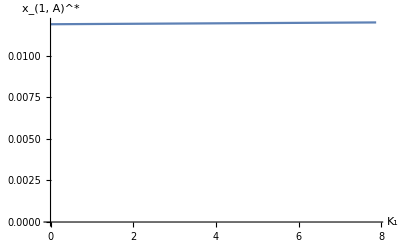

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{k,0,θ/(α+2η k0)},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"K_1","x_(1, A)^*"}]
]
```

#### - α

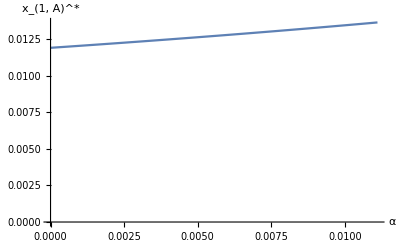

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{α,0,Min[{θ/k,1/k0}]},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"α","x_(1, A)^*"}]
]
```

#### - η

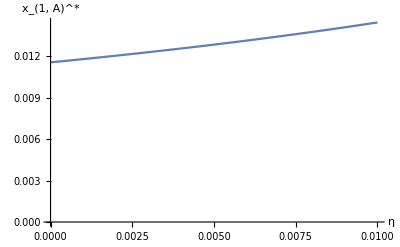

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{η,0,α},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"η","x_(1, A)^*"}]
]
```

#### - δ

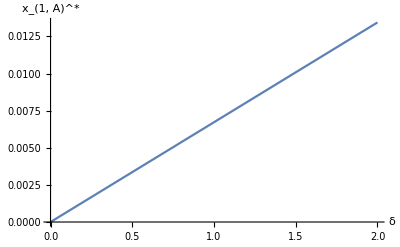

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{δ,0,2},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"δ","x_(1, A)^*"}]
]
```

#### - θ

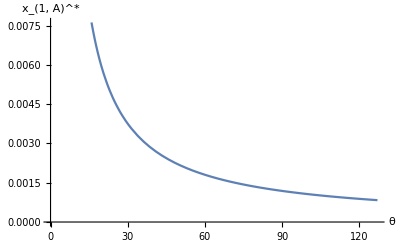

```mathematica
Show[Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η]},{θ,k(α+2η k0),10},PlotLegends->"Placeholder",AxesOrigin->{0,0},AxesLabel->{"θ","x_(1, A)^*"}]
]
```